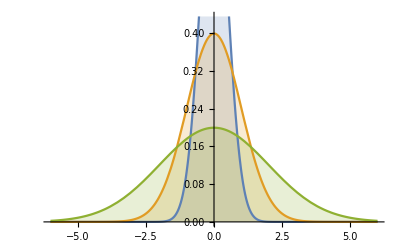

```mathematica
Plot[Table[PDF[NormalDistribution[0,σ],x],{σ,{0.5,1,2}}]//Evaluate,{x,-6,6},Filling->Axis]
```

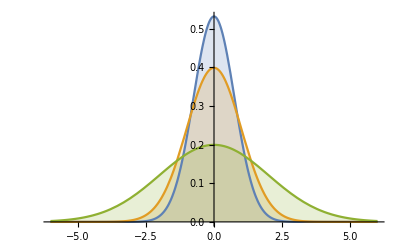

```mathematica
Plot[PDF[NormalDistribution[0,π/3]],Filling->Axis]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[PDF[NormalDistribution[0,π/3]],Filling→Axis]

```mathematica
θlist = RandomVariate[NormalDistribution[0,π/3],30]
```

{-0.216174,0.157545,0.39753,-0.16546,0.649833,-1.45098,0.750066,-0.236417,-0.866483,-0.441764,-1.98177,-1.6572,-1.14426,-1.02952,0.553372,-0.668077,0.357498,-0.234012,-0.571442,1.6219,-0.543606,-0.0542111,0.95384,-0.418403,-0.450808,-1.89911,0.0835546,0.438301,-0.328418,0.644979}

```mathematica
rlist = RandomReal[{0,1},30];
```

```mathematica
rθlist = Table[{rlist⟦i⟧ Cos[θlist⟦i⟧],rlist⟦i⟧Sin[θlist⟦i⟧]},{i,1,30}]
```

{{0.236017,-0.0518306},{0.492905,0.0783034},{0.649316,0.272638},{0.889122,-0.148472},{0.111383,0.0846447},{0.0780782,-0.648503},{0.487618,0.454324},{0.204794,-0.0493393},{0.517684,-0.609263},{0.0940003,-0.0444562},{-0.123392,-0.283147},{-0.0847285,-0.978139},{0.311365,-0.685164},{0.324346,-0.539525},{0.761208,0.470239},{0.458209,-0.361586},{0.596048,0.222653},{0.0765139,-0.0182393},{0.455293,-0.292756},{-0.0150512,0.29425},{0.435781,-0.263361},{0.528411,-0.0286739},{0.0473414,0.0667416},{0.892551,-0.39688},{0.461383,-0.223334},{-0.114728,-0.336799},{0.891332,0.0746487},{0.875257,0.410239},{0.398049,-0.135639},{0.739837,0.556588}}

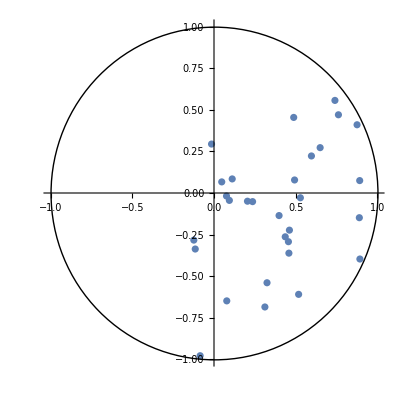

```mathematica
Show[ListPlot[rθlist],Graphics[Circle[]],PlotRange-> All, AspectRatio-> 1]
```

```mathematica
data=RandomVariate[BetaDistribution[3,2.5],10^4];
```

```mathematica
Show[Plot[PDF[BetaDistribution[5,5],(x+π)/(2*π)],{x,-π,π},PlotStyle->Thick]]
```

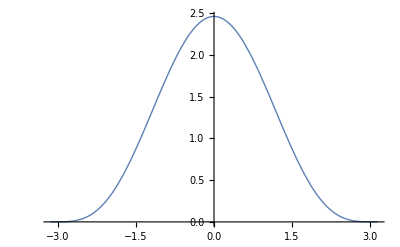

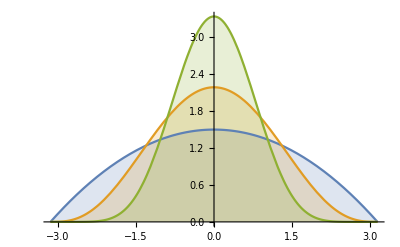

```mathematica
Plot[Table[PDF[BetaDistribution[σ,σ],(x+π)/(2*π)],{σ,{2,4,9}}]//Evaluate,{x,-π,π},Filling->Axis]
```

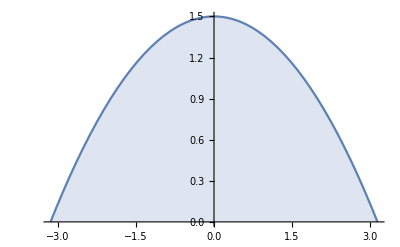

```mathematica
Plot[PDF[BetaDistribution[2,2],(x+π)/(2*π)]//Evaluate,{x,-π,π},Filling->Axis]
```